```mathematica
axis1:=Graphics[{Arrow[{{-Pi-0.8,0},{Pi+1.5,0}}], Text[Style[t,Large],{Pi+2.0,0}], Text[Style[Pi,Large],{Pi,-0.3}], Text[Style[-Pi,Large],{-Pi-0.2,-0.3}]}]
```

```mathematica
axis2e:=Graphics[{Arrow[{{0,-2.2},{0,(2*30+1)/(2Pi)+1}}],  
Text[Style["The Dirichlet Kernel D_N(t), N≤30Cell["",ExpressionUUID->"2c1e7e8d-be46-4926-b0d6-1ae2199e421c"]Cell["",ExpressionUUID->"781fd6c1-8bbc-44cd-a0d5-75a454e18a50"]"  , FontSize -> 20, Background -> LightRed], {0,(2*30+1)/(2Pi)+1.5}]}]
```

```mathematica
dots:=ListPlot[{{-Pi,0},{Pi,0}}, PlotStyle -> {Black, PointSize[Large]}, Axes -> False]
```

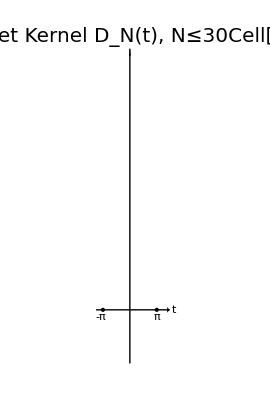

```mathematica
Show[axis1,axis2e,dots]
```

```mathematica
S[n_]:=Plot[1/(2Pi)+1/Pi Sum[Cos[k*t],{k,1,n}], {t,-Pi-0.5,Pi+0.5}, PlotStyle -> {Blue, Thick}, Axes -> False, PlotRange -> All]
```

```mathematica
Animate[Show[axis1,axis2e,dots,S[n]],{n,1,30}, AnimationRate ->3]
```

```mathematica
dirichelet:=Animate[Show[axis1,axis2e,dots,S[n]],{n,1,30}, AnimationRate ->3]
```

```mathematica
Export["dirichelet.mp4", dirichelet, "mp4" ]
```

dirichelet.mp4